# RR_LAB Projekt1

## Franciszek Pietrusiak

## Zadanie 1

Rozważmy równanie różniczkowe

a) podaj rozwiązanie ogólne powyższego równania

```mathematica
DSolve[y'[t]==(2 *t *y[t])/(t^2-y[t]^2),y[t],t]
```

{{y[t]→1/2 (ⅇ^C[1]-√(ⅇ^(2 C[1])-4 t^2))},{y[t]→1/2 (ⅇ^C[1]+√(ⅇ^(2 C[1])-4 t^2))}}

b) narysuj pole wektorowe odpowiadające powyższemu równaniu

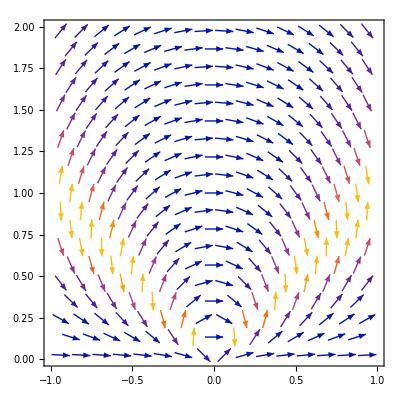

```mathematica
vecplot = VectorPlot[{1,(2* t* y)/(t^2-y^2)},{t,-1,1},{y,0,2}]
```

c) znajdź rozwiązanie powyższego równania z warunkiem początkowym y(0)=1

```mathematica
sol =DSolve[{y'[t]==(2* t* y[t])/(t^2-y[t]^2),y[0]==1},y[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{y[t]→1/2 (1+√(1-4 t^2))}}

d) umieść na jednym rysunku rozwiązanie powyższego równania z warunkiem początkowym y(0)=1 oraz pole wektorowe z punktu b)

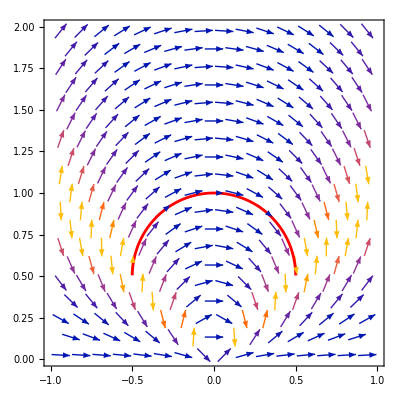

```mathematica
Show[vecplot, Plot[y[t] /. sol, {t,-1,1}, PlotStyle->Red]]
```

## Zadanie 2

Wahadłem matematycznym nazywamy punkt materialny o masie , zawieszony na długiej, cienkiej i nierozciągliwej nici. Wykonuje on wahania wokół najniżej położonego punktu , zwanego środkiem wahań. Wyprowadź równanie różniczkowe opisujące drgania wahadła.

Szukane równanie to:  , 
gdzie:
 to kąt odchylenia wahadła od pionu w chwili t,
 to przyspieszenie ziemskie. Zakładam, że 
  to długość nici. Zakładam, że .

a) narysuj pole wektorowe dla równania wahadła

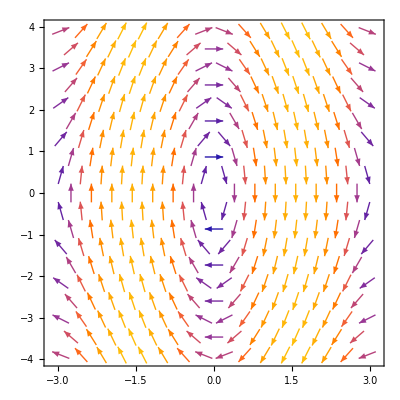

```mathematica
VectorPlot[{w,-9.8*Sin[θ]},{θ,-Pi,Pi},{w,-4,4}]
```

b) podaj rozwiązanie ogólne tego równania oraz narysuj pole wektorowe w przypadku gdy wahania są bardzo małe

```mathematica
DSolve[θ''[t]+9.8 *θ[t]==0,θ[t],t]
```

{{θ[t]→1. C[1] Cos[3.1305 t]+1. C[2] Sin[3.1305 t]}}

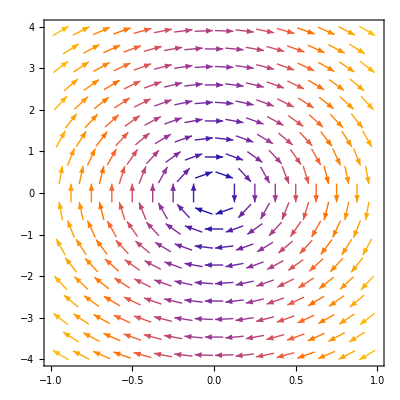

```mathematica
VectorPlot[{w,-9.81 θ},{θ,-1,1},{w,-4,4}]
```

c) znajdź rozwiązanie tego równania przy wybranym warunku początkowym, a następnie narysuj wykres tego rozwiązania przy założeniu, że wahania są bardzo małe.

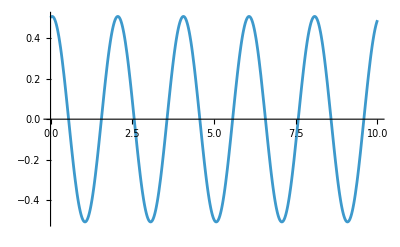

```mathematica
sol=DSolve[{θ''[t]+9.8* θ[t]==0,θ[0]==0.5,θ'[0]==0.25},θ[t],t];
Plot[θ[t]/. sol,{t,0,10}]
```

Założyłem, że warunkiem początkowym jest:  oraz .

## Zadanie 3

Rozważmy równanie różniczkowe

a) sprawdzić, czy funkcja  jest jego rozwiązaniem.

```mathematica
z1[x_]:=Log[x]
Simplify[x*D[z1[x],x] + z1[x] == z1[x]^2*Log[x]]
```

Log[x]^3==1+Log[x]

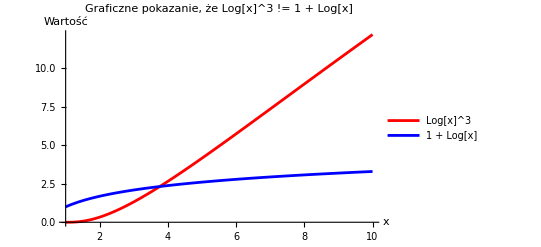

```mathematica
Plot[{Log[x]^3,1+Log[x]},{x,1,10},PlotStyle->{Red,Blue},PlotLegends->{"Log[x]^3","1 + Log[x]"},AxesLabel->{"x","Wartość"},PlotLabel->"Graficzne pokazanie, że Log[x]^3 != 1 + Log[x]"]
```

b) podaj rozwiązanie ogólne tego równania

```mathematica
DSolve[x*z'[x]+z[x]==z[x]^2* Log[x],z[x],x]
```

{{z[x]→1/(1+x C[1]+Log[x])}}

c) narysuj pole wektorowe dla tego równania

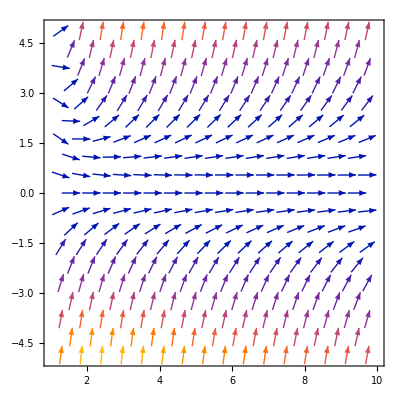

```mathematica
VectorPlot[{1,(z^2 *Log[x]-z)/x},{x,1,10},{z,-5,5}]
```

d) narysuj na jednym rysunku kilka rozwiązań tego równania przy różnych warunkach początkowych

NDSolve::ndsz: At x == 5.35669, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 3.28325, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 2.61504, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 2.28049, step size is effectively zero; singularity or stiff system suspected.

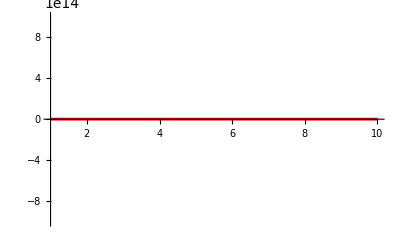

```mathematica
sol1=NDSolve[{x* z'[x]+z[x]==z[x]^2 *Log[x],z[1]==1},z,{x,1,10}];
sol2=NDSolve[{x* z'[x]+z[x]==z[x]^2 *Log[x],z[1]==2},z,{x,1,10}];
sol3=NDSolve[{x* z'[x]+z[x]==z[x]^2 *Log[x],z[1]==3},z,{x,1,10}];
sol4=NDSolve[{x* z'[x]+z[x]==z[x]^2 *Log[x],z[1]==4},z,{x,1,10}];
sol5=NDSolve[{x* z'[x]+z[x]==z[x]^2 *Log[x],z[1]==5},z,{x,1,10}];

Plot[Evaluate[{z[x]/. sol1,z[x]/. sol2,z[x]/. sol3, z[x] /. sol4, z[x] /. sol5}],{x,1,10},PlotStyle->{Red,Blue,Green, Pink,Brown}]
```